# Figure 7

Clicking Run all evaluates the whole notebook from top to bottom . Some computations may take a while, so please wait until all cells have finished running .

```mathematica
Button["Run all",
With[{nb=ButtonNotebook[]},
FrontEndTokenExecute[nb,"EvaluateNotebook"];
SelectionMove[nb,After,Notebook]
]
]
```

Run all

```mathematica
ClearAll["Global`*"];
terms=100;
AlphaMu[α_,μ_,𝓍_]:=ProbabilityDistribution[(α μ^μ)/Gamma[μ] x^(α μ-1)/𝓍^(α μ)Exp[-μ(x/𝓍)^α],{x,0,∞},Assumptions->α>0&&μ>0&&𝓍>0];
KappaMu[κ_,μ_,𝓎_]:=ProbabilityDistribution[(2(κ μ)^((1-μ)/2))/Exp[κ μ] y^μ/(𝓎/(√(μ(1+κ))))^(μ+1)Exp[-y^2/(𝓎/(√(μ(1+κ))))^2]BesselI[μ-1,2(√(κ μ)y)/(𝓎/(√(μ(1+κ))))],{y,0,∞},Assumptions->κ>0&&μ>0&&𝓎>0];
EtaMu[eta_,mu_,p_,zhat_,n_]:=Module[{s2,g1,g2},s2=zhat^2 eta (1+p)/(mu p (1+eta));
g1=RandomVariate[GammaDistribution[mu/(1+p),p s2/eta],n];
g2=RandomVariate[GammaDistribution[mu p/(1+p),s2],n];
Sqrt[g1+g2]];
Eam[α_,μ_,𝓍_,n_,k_]:=(𝓍^n Gamma[μ+n/α]/(μ^(n/α)Gamma[μ]))^k;
Ekm[κ_,μ_,𝓎_,n_,k_]:=(Gamma[μ+n/2]/Gamma[μ](𝓎/(√(μ(1+κ))))^n Hypergeometric1F1[-n/2,μ,-κ μ])^k;
Eem[η_,μ_,p_,𝓏_,n_,k_]:=(Gamma[μ+n/2]/Gamma[μ](𝓏 √((η(1+p))/(μ p(1+η))))^n Hypergeometric2F1[-n/2,μ/(1+p),μ,1-p/η])^k;

AlphaMuDist[α_,μ_,𝓍_,x_]:=(α μ^μ)/Gamma[μ] x^(α μ-1)/𝓍^(α μ)Exp[-μ(x/𝓍)^α];
(* Functions for moment matching *)
EEa[n_,α_,μ_,rs_]:=Eam[α[[1]],μ[[1]],rs[[1]],n,1]*Eam[α[[2]],μ[[2]],rs[[2]],n,1];
EEk[n_,κ_,μ_,rs_]:=Ekm[κ[[1]],μ[[1]],rs[[1]],n,1]*Ekm[κ[[2]],μ[[2]],rs[[2]],n,1];
EEe[n_,η_,μ_,p_,rs_]:=Eem[η[[1]],μ[[1]],p[[1]],rs[[1]],n,1]*Eem[η[[2]],μ[[2]],p[[2]],rs[[2]],n,1];
EYa1[αs_,μs_,rs_,L_]:=L*(EEa[1,αs,μs,rs]);
EYk1[κs_,μs_,rs_,L_]:=L*(EEk[1,κs,μs,rs]);
EYe1[ηs_,μs_,ps_,rs_,L_]:=L*(EEe[1,ηs,μs,ps,rs]);
EYa20[n_,αs_,μs_,rs_]:=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 ∑_(n10=0)^n9 ∑_(n11=0)^n10 ∑_(n12=0)^n11 ∑_(n13=0)^n12 ∑_(n14=0)^n13 ∑_(n15=0)^n14 ∑_(n16=0)^n15 ∑_(n17=0)^n16 ∑_(n18=0)^n17 ∑_(n19=0)^n18 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9]Binomial[n9,n10]Binomial[n10,n11]Binomial[n11,n12]Binomial[n12,n13]Binomial[n13,n14]Binomial[n14,n15]Binomial[n15,n16]Binomial[n16,n17]Binomial[n17,n18]Binomial[n18,n19](EEa[n-n1,αs,μs,rs])(EEa[n1-n2,αs,μs,rs])(EEa[n2-n3,αs,μs,rs])(EEa[n3-n4,αs,μs,rs])(EEa[n4-n5,αs,μs,rs])(EEa[n5-n6,αs,μs,rs])(EEa[n6-n7,αs,μs,rs])(EEa[n7-n8,αs,μs,rs])(EEa[n8-n9,αs,μs,rs])(EEa[n9-n10,αs,μs,rs])(EEa[n10-n11,αs,μs,rs])(EEa[n11-n12,αs,μs,rs])(EEa[n12-n13,αs,μs,rs])(EEa[n13-n14,αs,μs,rs])(EEa[n14-n15,αs,μs,rs])(EEa[n15-n16,αs,μs,rs])(EEa[n16-n17,αs,μs,rs])(EEa[n17-n18,αs,μs,rs])(EEa[n18-n19,αs,μs,rs])(EEa[n19,αs,μs,rs]);
EYk40[n_,κs_,μs_,rs_]:=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 ∑_(n10=0)^n9 ∑_(n11=0)^n10 ∑_(n12=0)^n11 ∑_(n13=0)^n12 ∑_(n14=0)^n13 ∑_(n15=0)^n14 ∑_(n16=0)^n15 ∑_(n17=0)^n16 ∑_(n18=0)^n17 ∑_(n19=0)^n18 ∑_(n20=0)^n19 ∑_(n21=0)^n20 ∑_(n22=0)^n21 ∑_(n23=0)^n22 ∑_(n24=0)^n23 ∑_(n25=0)^n24 ∑_(n26=0)^n25 ∑_(n27=0)^n26 ∑_(n28=0)^n27 ∑_(n29=0)^n28 ∑_(n30=0)^n29 ∑_(n31=0)^n30 ∑_(n32=0)^n31 ∑_(n33=0)^n32 ∑_(n34=0)^n33 ∑_(n35=0)^n34 ∑_(n36=0)^n35 ∑_(n37=0)^n36 ∑_(n38=0)^n37 ∑_(n39=0)^n38 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9]Binomial[n9,n10]Binomial[n10,n11]Binomial[n11,n12]Binomial[n12,n13]Binomial[n13,n14]Binomial[n14,n15]Binomial[n15,n16]Binomial[n16,n17]Binomial[n17,n18]Binomial[n18,n19]Binomial[n19,n20]Binomial[n20,n21]Binomial[n21,n22]Binomial[n22,n23]Binomial[n23,n24]Binomial[n24,n25]Binomial[n25,n26]Binomial[n26,n27]Binomial[n27,n28]Binomial[n28,n29]Binomial[n29,n30]Binomial[n30,n31]Binomial[n31,n32]Binomial[n32,n33]Binomial[n33,n34]Binomial[n34,n35]Binomial[n35,n36]Binomial[n36,n37]Binomial[n37,n38]Binomial[n38,n39](EEk[n-n1,κs,μs,rs])(EEk[n1-n2,κs,μs,rs])(EEk[n2-n3,κs,μs,rs])(EEk[n3-n4,κs,μs,rs])(EEk[n4-n5,κs,μs,rs])(EEk[n5-n6,κs,μs,rs])(EEk[n6-n7,κs,μs,rs])(EEk[n7-n8,κs,μs,rs])(EEk[n8-n9,κs,μs,rs])(EEk[n9-n10,κs,μs,rs])(EEk[n10-n11,κs,μs,rs])(EEk[n11-n12,κs,μs,rs])(EEk[n12-n13,κs,μs,rs])(EEk[n13-n14,κs,μs,rs])(EEk[n14-n15,κs,μs,rs])(EEk[n15-n16,κs,μs,rs])(EEk[n16-n17,κs,μs,rs])(EEk[n17-n18,κs,μs,rs])(EEk[n18-n19,κs,μs,rs])(EEk[n19-n20,κs,μs,rs])(EEk[n20-n21,κs,μs,rs])(EEk[n21-n22,κs,μs,rs])(EEk[n22-n23,κs,μs,rs])(EEk[n23-n24,κs,μs,rs])(EEk[n24-n25,κs,μs,rs])(EEk[n25-n26,κs,μs,rs])(EEk[n26-n27,κs,μs,rs])(EEk[n27-n28,κs,μs,rs])(EEk[n28-n29,κs,μs,rs])(EEk[n29-n30,κs,μs,rs])(EEk[n30-n31,κs,μs,rs])(EEk[n31-n32,κs,μs,rs])(EEk[n32-n33,κs,μs,rs])(EEk[n33-n34,κs,μs,rs])(EEk[n34-n35,κs,μs,rs])(EEk[n35-n36,κs,μs,rs])(EEk[n36-n37,κs,μs,rs])(EEk[n37-n38,κs,μs,rs])(EEk[n38-n39,κs,μs,rs])(EEk[n39,κs,μs,rs]);
EYe30[n_,ηs_,μs_,ps_,rs_]:=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 ∑_(n10=0)^n9 ∑_(n11=0)^n10 ∑_(n12=0)^n11 ∑_(n13=0)^n12 ∑_(n14=0)^n13 ∑_(n15=0)^n14 ∑_(n16=0)^n15 ∑_(n17=0)^n16 ∑_(n18=0)^n17 ∑_(n19=0)^n18 ∑_(n20=0)^n19 ∑_(n21=0)^n20 ∑_(n22=0)^n21 ∑_(n23=0)^n22 ∑_(n24=0)^n23 ∑_(n25=0)^n24 ∑_(n26=0)^n25 ∑_(n27=0)^n26 ∑_(n28=0)^n27 ∑_(n29=0)^n28 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9]Binomial[n9,n10]Binomial[n10,n11]Binomial[n11,n12]Binomial[n12,n13]Binomial[n13,n14]Binomial[n14,n15]Binomial[n15,n16]Binomial[n16,n17]Binomial[n17,n18]Binomial[n18,n19]Binomial[n19,n20]Binomial[n20,n21]Binomial[n21,n22]Binomial[n22,n23]Binomial[n23,n24]Binomial[n24,n25]Binomial[n25,n26]Binomial[n26,n27]Binomial[n27,n28]Binomial[n28,n29](EEe[n-n1,ηs,μs,ps,rs])(EEe[n1-n2,ηs,μs,ps,rs])(EEe[n2-n3,ηs,μs,ps,rs])(EEe[n3-n4,ηs,μs,ps,rs])(EEe[n4-n5,ηs,μs,ps,rs])(EEe[n5-n6,ηs,μs,ps,rs])(EEe[n6-n7,ηs,μs,ps,rs])(EEe[n7-n8,ηs,μs,ps,rs])(EEe[n8-n9,ηs,μs,ps,rs])(EEe[n9-n10,ηs,μs,ps,rs])(EEe[n10-n11,ηs,μs,ps,rs])(EEe[n11-n12,ηs,μs,ps,rs])(EEe[n12-n13,ηs,μs,ps,rs])(EEe[n13-n14,ηs,μs,ps,rs])(EEe[n14-n15,ηs,μs,ps,rs])(EEe[n15-n16,ηs,μs,ps,rs])(EEe[n16-n17,ηs,μs,ps,rs])(EEe[n17-n18,ηs,μs,ps,rs])(EEe[n18-n19,ηs,μs,ps,rs])(EEe[n19-n20,ηs,μs,ps,rs])(EEe[n20-n21,ηs,μs,ps,rs])(EEe[n21-n22,ηs,μs,ps,rs])(EEe[n22-n23,ηs,μs,ps,rs])(EEe[n23-n24,ηs,μs,ps,rs])(EEe[n24-n25,ηs,μs,ps,rs])(EEe[n25-n26,ηs,μs,ps,rs])(EEe[n26-n27,ηs,μs,ps,rs])(EEe[n27-n28,ηs,μs,ps,rs])(EEe[n28-n29,ηs,μs,ps,rs])(EEe[n29,ηs,μs,ps,rs]);
EHa[n_,α_,μ_,rs_,func_]:=∑_(n1=0)^n Binomial[n,n1]Eam[α[[1]],μ[[1]],rs[[1]],n-n1,1]func[n1,{α[[2]],α[[3]]},{μ[[2]],μ[[3]]},{rs[[2]],rs[[3]]}];
EHa1[α_,μ_,rs_,L_,func_]:=Eam[α[[1]],μ[[1]],rs[[1]],1,1]+func[{α[[2]],α[[3]]},{μ[[2]],μ[[3]]},{rs[[2]],rs[[3]]},L];
EHk[n_,κ_,μ_,rs_,func_]:=∑_(n1=0)^n Binomial[n,n1]Ekm[κ[[1]],μ[[1]],rs[[1]],n-n1,1]func[n1,{κ[[2]],κ[[3]]},{μ[[2]],μ[[3]]},{rs[[2]],rs[[3]]}];
EHk1[κ_,μ_,rs_,L_,func_]:=Ekm[κ[[1]],μ[[1]],rs[[1]],1,1]+func[{κ[[2]],κ[[3]]},{μ[[2]],μ[[3]]},{rs[[2]],rs[[3]]},L];
EHe[n_,η_,μ_,p_,rs_,func_]:=∑_(n1=0)^n Binomial[n,n1]Eem[η[[1]],μ[[1]],p[[1]],rs[[1]],n-n1,1]func[n1,{η[[2]],η[[3]]},{μ[[2]],μ[[3]]},{p[[2]],p[[3]]},{rs[[2]],rs[[3]]}];
EHe1[α_,μ_,p_,rs_,L_,func_]:=Eem[α[[1]],μ[[1]],p[[1]],rs[[1]],1,1]+func[{α[[2]],α[[3]]},{μ[[2]],μ[[3]]},{p[[2]],p[[3]]},{rs[[2]],rs[[3]]},L];
(* For the Three Fading environment *)
EEka[n_,κ_,μκ_,α_,μα_,rs_]:=Ekm[κ,μκ,rs[[1]],n,1]*Eam[α,μα,rs[[2]],n,1];
EYka1[κ_,μκ_,α_,μα_,rs_,L_]:=L*EEka[1,κ,μκ,α,μα,rs];
EYka10[n_,κs_,μκs_,αs_,μαs_,rs_]:=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9](EEka[n-n1,κs,μκs,αs,μαs,rs])(EEka[n1-n2,κs,μκs,αs,μαs,rs])(EEka[n2-n3,κs,μκs,αs,μαs,rs])(EEka[n3-n4,κs,μκs,αs,μαs,rs])(EEka[n4-n5,κs,μκs,αs,μαs,rs])(EEka[n5-n6,κs,μκs,αs,μαs,rs])(EEka[n6-n7,κs,μκs,αs,μαs,rs])(EEka[n7-n8,κs,μκs,αs,μαs,rs])(EEka[n8-n9,κs,μκs,αs,μαs,rs])(EEka[n9,κs,μκs,αs,μαs,rs]);
EHkae[n_,η_,μ_,p_,r_,κ_,μκ_,α_,μα_,rs_,func_]:=∑_(n1=0)^n Binomial[n,n1]Eem[η,μ,p,r,n-n1,1]func[n1,κ,μκ,α,μα,rs];
EHkae1[η_,μ_,p_,r_,κ_,μκ_,α_,μα_,rs_,L_,func_]:=Eem[η,μ,p,r,1,1]+func[κ,μκ,α,μα,rs,L];
```

```mathematica
(* α-μ *)
```

```mathematica
Subscript[L, α]=20;
Subscript[L, κ]=40;
Subscript[L, η]=30;
Subscript[L, ηκα]=10;
Table[{Subscript[α, T,i],Subscript[μ, T,i,α]}={16/10,7/10},{i,Subscript[L, α]}];
Table[{Subscript[α, i,R],Subscript[μ, i,R,α]}={24/10,13/10},{i,Subscript[L, α]}];
{Subscript[α, T,R],Subscript[μ, T,R,α]}={8/10,11/10};
Subscript[r̂, T,R]=1;
Subscript[𝒜, T,R]=Subscript[r̂, T,R]/Subscript[μ, T,R,α]^(1/Subscript[α, T,R]);
Table[{Subscript[r̂, T,i],Subscript[r̂, i,R]}={1,1},{i,Subscript[L, α]}];
Table[{Subscript[𝒜, T,i],Subscript[𝒜, i,R]}={Subscript[r̂, T,i]/Subscript[μ, T,i,α]^(1/Subscript[α, T,i]),Subscript[r̂, i,R]/Subscript[μ, i,R,α]^(1/Subscript[α, i,R])},{i,Subscript[L, α]}];
Table[Subscript[αμ, Subscript[m, i]]=Min[Subscript[α, T,i] Subscript[μ, T,i,α],Subscript[α, i,R] Subscript[μ, i,R,α]],{i,Subscript[L, α]}];
Table[Subscript[αμ, Subscript[M, i]]=Max[Subscript[α, T,i] Subscript[μ, T,i,α],Subscript[α, i,R] Subscript[μ, i,R,α]],{i,Subscript[L, α]}];
Table[Subscript[α, Subscript[m, i]]=MinimalBy[{{Subscript[α, T,i],Subscript[α, T,i] Subscript[μ, T,i,α]},{Subscript[α, i,R],Subscript[α, i,R] Subscript[μ, i,R,α]}},Last][[1,1]],{i,Subscript[L, α]}];
Table[Subscript[α, Subscript[M, i]]=MaximalBy[{{Subscript[α, T,i],Subscript[α, T,i] Subscript[μ, T,i,α]},{Subscript[α, i,R],Subscript[α, i,R] Subscript[μ, i,R,α]}},Last][[1,1]],{i,Subscript[L, α]}];
Table[Subscript[ak, i]=Subscript[α, T,R] Subscript[μ, T,R,α]+∑_(j=1)^Subscript[L, α] Subscript[αμ, Subscript[m, j]],{i,1}];
```

```mathematica
(* Monte-Carlo of Sums *)
SeedRandom[123];
samples=10^6;
Timing[
Table[Subscript[h, T,i,α]=RandomVariate[GammaDistribution[Subscript[μ, T,i,α],Subscript[r̂, T,i]/Subscript[μ, T,i,α]^(1/Subscript[α, T,i]),Subscript[α, T,i],0],samples],{i,Subscript[L, α]}];
Table[Subscript[h, i,R,α]=RandomVariate[GammaDistribution[Subscript[μ, i,R,α],Subscript[r̂, i,R]/Subscript[μ, i,R,α]^(1/Subscript[α, i,R]),Subscript[α, i,R],0],samples],{i,Subscript[L, α]}];
Subscript[h, T,R,α]=RandomVariate[GammaDistribution[Subscript[μ, T,R,α],Subscript[r̂, T,R]/Subscript[μ, T,R,α]^(1/Subscript[α, T,R]),Subscript[α, T,R],0],samples];]
```

{3.09375,Null}

```mathematica
Table[{Subscript[Y, α,i],Subscript[H, α,i]}={∑_(j=1)^Subscript[L, α] Subscript[h, T,j,α] Subscript[h, j,R,α],Subscript[h, T,R,α]+∑_(j=1)^Subscript[L, α] Subscript[h, T,j,α] Subscript[h, j,R,α]},{i,1}];
```

```mathematica
R2vl=Table[0,{1}];R4vl=Table[0,{1}];
R1vl=Table[0,{1}];
R2vl[[1]]=EHa[2,{Subscript[α, T,R],Subscript[α, T,1],Subscript[α, 1,R]},{Subscript[μ, T,R,α],Subscript[μ, T,1,α],Subscript[μ, 1,R,α]},{Subscript[r̂, T,R],Subscript[r̂, T,1],Subscript[r̂, 1,R]},EYa20];
R4vl[[1]]=EHa[4,{Subscript[α, T,R],Subscript[α, T,1],Subscript[α, 1,R]},{Subscript[μ, T,R,α],Subscript[μ, T,1,α],Subscript[μ, 1,R,α]},{Subscript[r̂, T,R],Subscript[r̂, T,1],Subscript[r̂, 1,R]},EYa20];
Table[R1vl[[i]]=EHa1[{Subscript[α, T,R],Subscript[α, T,1],Subscript[α, 1,R]},{Subscript[μ, T,R,α],Subscript[μ, T,1,α],Subscript[μ, 1,R,α]},{Subscript[r̂, T,R],Subscript[r̂, T,1],Subscript[r̂, 1,R]},Subscript[L, α],EYa1],{i,1}];
```

```mathematica
roots={{1,3},{1,2},{1,3}};
For[j=1,j≤1,j++,
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1vl[[j]])^2/((R2vl[[j]])-(R1vl[[j]])^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2vl[[j]])^2/((R4vl[[j]])-(R2vl[[j]])^2)},{{μ,roots[[j,1]]},{α,roots[[j,2]]}},WorkingPrecision->40];
Subscript[r̂, h,j,α]=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1vl[[j]]))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
Subscript[μ, h,j,α]=Sol[[1,2]];
Subscript[α, h,j,α]=Sol[[2,2]];
];
Table[Subscript[α, h,i,α],{i,1}]
Table[Subscript[μ, h,i,α],{i,1}]
Table[Subscript[r̂, h,i,α],{i,1}]
```

{0.685228948316881972991885240460510556075}

{50.25446920589508563944195035850840825221}

{16.69126706719837370614934303254540675}

```mathematica
(* κ-μ *)
```

```mathematica
Table[{Subscript[κ, T,i],Subscript[μ, T,i,κ]}={7/10,4/10},{i,Subscript[L, κ]}];
Table[{Subscript[κ, i,R],Subscript[μ, i,R,κ]}={4/10,3/10},{i,Subscript[L, κ]}];
{Subscript[κ, T,R],Subscript[μ, T,R,κ]}={5/10,8/10};
Subscript[r̂, T,R]=1;
Subscript[𝒦, T,R]=Subscript[r̂, T,R]/(√(Subscript[μ, T,R,κ](1+Subscript[κ, T,R])));
Table[{Subscript[r̂, T,i],Subscript[r̂, i,R]}={1,1},{i,Subscript[L, κ]}];
Table[{Subscript[𝒦, T,i],Subscript[𝒦, i,R]}={Subscript[r̂, T,i]/(√(Subscript[μ, T,i,κ](1+Subscript[κ, T,i]))),Subscript[r̂, i,R]/(√(Subscript[μ, i,R,κ](1+Subscript[κ, i,R])))},{i,Subscript[L, κ]}];
Table[Subscript[μ, m,i,κ]=Min[Subscript[μ, T,i,κ],Subscript[μ, i,R,κ]],{i,Subscript[L, κ]}];
```

```mathematica
(* Monte-Carlo of Sums *)
SeedRandom[123];
samples=10^6;
Timing[
Table[Subscript[h, T,i,κ]=RandomVariate[RiceDistribution[Subscript[μ, T,i,κ],(Subscript[r̂, T,i] √(Subscript[κ, T,j] (1+Subscript[κ, T,i])))/(1+Subscript[κ, T,i]),Subscript[r̂, T,i]/(√(2+2 Subscript[κ, T,i]))],samples],{i,Subscript[L, κ]}];
Table[Subscript[h, i,R,κ]=RandomVariate[RiceDistribution[Subscript[μ, i,R,κ],(Subscript[r̂, i,R] √(Subscript[κ, i,R] (1+Subscript[κ, i,R])))/(1+Subscript[κ, i,R]),Subscript[r̂, i,R]/(√(2+2 Subscript[κ, i,R]))],samples],{i,Subscript[L, κ]}];
Subscript[h, T,R,κ]=RandomVariate[RiceDistribution[Subscript[μ, T,R,κ],(Subscript[r̂, T,R] √(Subscript[κ, T,R](1+Subscript[κ, T,R])))/(1+Subscript[κ, T,R]),Subscript[r̂, T,R]/(√(2+2 Subscript[κ, T,R]))],samples];]
```

{37.7344,Null}

```mathematica
Table[{Subscript[Y, κ,i],Subscript[H, κ,i]}={∑_(j=1)^Subscript[L, κ] Subscript[h, T,j,κ] Subscript[h, j,R,κ],Subscript[h, T,R,κ]+∑_(j=1)^Subscript[L, κ] Subscript[h, T,j,κ] Subscript[h, j,R,κ]},{i,1}];
```

```mathematica
R2vl=Table[0,{1}];R4vl=Table[0,{1}];
R1vl=Table[0,{1}];
R2vl[[1]]=EHk[2,{Subscript[κ, T,R],Subscript[κ, T,1],Subscript[κ, 1,R]},{Subscript[μ, T,R,κ],Subscript[μ, T,1,κ],Subscript[μ, 1,R,κ]},{Subscript[r̂, T,R],Subscript[r̂, T,1],Subscript[r̂, 1,R]},EYk40];
R4vl[[1]]=EHk[4,{Subscript[κ, T,R],Subscript[κ, T,1],Subscript[κ, 1,R]},{Subscript[μ, T,R,κ],Subscript[μ, T,1,κ],Subscript[μ, 1,R,κ]},{Subscript[r̂, T,R],Subscript[r̂, T,1],Subscript[r̂, 1,R]},EYk40];
Table[R1vl[[i]]=EHk1[{Subscript[κ, T,R],Subscript[κ, T,1],Subscript[κ, 1,R]},{Subscript[μ, T,R,κ],Subscript[μ, T,1,κ],Subscript[μ, 1,R,κ]},{Subscript[r̂, T,R],Subscript[r̂, T,1],Subscript[r̂, 1,R]},Subscript[L, κ],EYk1],{i,1}];
```

```mathematica
roots={{1,5},{1,5},{1,2}};
For[j=1,j≤1,j++,
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1vl[[j]])^2/((R2vl[[j]])-(R1vl[[j]])^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2vl[[j]])^2/((R4vl[[j]])-(R2vl[[j]])^2)},{{μ,roots[[j,2]]},{α,roots[[j,2]]}},WorkingPrecision->30];
Subscript[r̂, h,j,κ]=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1vl[[j]]))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
Subscript[μ, h,j,κ]=Sol[[1,2]];
Subscript[α, h,j,κ]=Sol[[2,2]];
];
Table[Subscript[α, h,i,κ],{i,1}]//N
Table[Subscript[μ, h,i,κ],{i,1}]//N
Table[Subscript[r̂, h,i,κ],{i,1}]//N
```

{0.978954}

{20.3262}

{23.2292}

```mathematica
(* Extended η-μ *)
```

```mathematica
Table[{Subscript[η, T,i],Subscript[μ, T,i,η],Subscript[p, T,i]}={7/10,15/10,1/10},{i,Subscript[L, η]}];
Table[{Subscript[η, i,R],Subscript[μ, i,R,η],Subscript[p, i,R]}={12/10,11/10,3/10},{i,Subscript[L, η]}];
{Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R]}={15/10,9/10,5/10};
Subscript[r̂, T,R]=1;

Subscript[ξ, T,R]=(1+Subscript[η, T,R])/(1+Subscript[p, T,R]);
Table[{Subscript[r̂, T,i],Subscript[r̂, i,R]}={1,1},{i,Subscript[L, η]}];
Table[{Subscript[ξ, T,i],Subscript[ξ, i,R]}={(1+Subscript[η, T,i])/(1+Subscript[p, T,i]),(1+Subscript[η, i,R])/(1+Subscript[p, i,R])},{i,Subscript[L, η]}];
Table[Subscript[μ, m,i,η]=Min[Subscript[μ, T,i,η],Subscript[μ, i,R,η]],{i,Subscript[L, η]}];
```

```mathematica
(* Monte-Carlo of Sums *)
SeedRandom[123];
samples=10^6;
Timing[
Table[Subscript[h, T,i,η]=EtaMu[Subscript[η, T,i],Subscript[μ, T,i,η],Subscript[p, T,i],Subscript[r̂, T,i],samples],{i,Subscript[L, η]}];
Table[Subscript[h, i,R,η]=EtaMu[Subscript[η, i,R],Subscript[μ, i,R,η],Subscript[p, i,R],Subscript[r̂, i,R],samples],{i,Subscript[L, η]}];
Subscript[h, T,R,η]=EtaMu[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],samples];]
```

{9.53125,Null}

```mathematica
Table[{Subscript[Y, η,i],Subscript[H, η,i]}={∑_(j=1)^Subscript[L, η] Subscript[h, T,j,η] Subscript[h, j,R,η],Subscript[h, T,R,η]+∑_(j=1)^Subscript[L, η] Subscript[h, T,j,η] Subscript[h, j,R,η]},{i,1}];
```

```mathematica
R2vl=Table[0,{1}];R4vl=Table[0,{1}];
R1vl=Table[0,{1}];
R2vl[[1]]=EHe[2,{Subscript[η, T,R],Subscript[η, T,1],Subscript[η, 1,R]},{Subscript[μ, T,R,η],Subscript[μ, T,1,η],Subscript[μ, 1,R,η]},{Subscript[p, T,R],Subscript[p, T,1],Subscript[p, 1,R]},{Subscript[r̂, T,R],Subscript[r̂, T,1],Subscript[r̂, 1,R]},EYe30];
R4vl[[1]]=EHe[4,{Subscript[η, T,R],Subscript[η, T,1],Subscript[η, 1,R]},{Subscript[μ, T,R,η],Subscript[μ, T,1,η],Subscript[μ, 1,R,η]},{Subscript[p, T,R],Subscript[p, T,1],Subscript[p, 1,R]},{Subscript[r̂, T,R],Subscript[r̂, T,1],Subscript[r̂, 1,R]},EYe30];
Table[R1vl[[i]]=EHe1[{Subscript[η, T,R],Subscript[η, T,1],Subscript[η, 1,R]},{Subscript[μ, T,R,η],Subscript[μ, T,1,η],Subscript[μ, 1,R,η]},{Subscript[p, T,R],Subscript[p, T,1],Subscript[p, 1,R]},{Subscript[r̂, T,R],Subscript[r̂, T,1],Subscript[r̂, 1,R]},Subscript[L, η],EYe1],{i,1}];
```

```mathematica
roots={{4,90},{5,2},{5,2}};
For[j=1,j≤1,j++,
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1vl[[j]])^2/((R2vl[[j]])-(R1vl[[j]])^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2vl[[j]])^2/((R4vl[[j]])-(R2vl[[j]])^2)},{{μ,roots[[j,1]]},{α,roots[[j,2]]}},WorkingPrecision->40];
Subscript[r̂, h,j,η]=Re[((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1vl[[j]]))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]])];
Subscript[μ, h,j,η]=Sol[[1,2]];
Subscript[α, h,j,η]=Sol[[2,2]];
];
Table[Subscript[α, h,i,η],{i,1}]
Table[Subscript[μ, h,i,η],{i,1}]
Table[Subscript[r̂, h,i,η],{i,1}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.3290635543140831988253627728456162418868}

{426.0202355096241430508801914357198382065}

{23.7808251473652644630455730963299379}

General::munfl: 0.000715^139.187732906519720049724192118034105656 is too small to represent as a normalized machine number; precision may be lost.

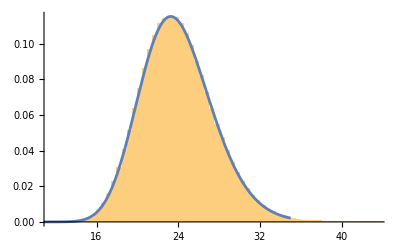

```mathematica
val=1;
Show[Histogram[Subscript[H, η,val],100,"PDF"],Plot[PDF[AlphaMu[Subscript[α, h,val,η],Subscript[μ, h,val,η],Subscript[r̂, h,val,η]],x],{x,0,35}]]
```

```mathematica
(* Three Fading Ext.η-μ,κ-μ,α-μ *)
```

```mathematica
Table[{Subscript[κ, T,i],Subscript[μ, T,i,κ]}={18/10,6/10},{i,Subscript[L, ηκα]}];
Table[{Subscript[α, i,R],Subscript[μ, i,R,α]}={18/10,15/10},{i,Subscript[L, ηκα]}];
{Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R]}={15/10,9/10,5/10};
Subscript[r̂, T,R]=1;

Subscript[ξ, T,R]=(1+Subscript[η, T,R])/(1+Subscript[p, T,R]);
Table[{Subscript[r̂, T,i],Subscript[r̂, i,R]}={1,1},{i,Subscript[L, ηκα]}];
Table[{Subscript[𝒦, T,i],Subscript[𝒜, i,R]}={Subscript[r̂, T,i]/(√(Subscript[μ, T,i,κ](1+Subscript[κ, T,i]))),Subscript[r̂, i,R]/Subscript[μ, i,R,α]^(1/Subscript[α, i,R])},{i,Subscript[L, ηκα]}];
```

```mathematica
(* Monte-Carlo of Sums *)
SeedRandom[123];
samples=10^6;
Timing[
Table[Subscript[h, T,i,ηκα]=RandomVariate[RiceDistribution[Subscript[μ, T,i,κ],(Subscript[r̂, T,i] √(Subscript[κ, T,i](1+Subscript[κ, T,i])))/(1+Subscript[κ, T,i]),Subscript[r̂, T,i]/(√(2+2 Subscript[κ, T,i]))],samples],{i,Subscript[L, ηκα]}];
Table[Subscript[h, i,R,ηκα]=RandomVariate[AlphaMu[Subscript[α, i,R],Subscript[μ, i,R,α],Subscript[r̂, i,R]],samples],{i,Subscript[L, ηκα]}];
Subscript[h, T,R,ηκα]=EtaMu[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],samples];]
```

{14.3906,Null}

```mathematica
Table[{Subscript[Y, ηκα,i],Subscript[H, ηκα,i]}={∑_(j=1)^Subscript[L, ηκα] Subscript[h, T,j,ηκα] Subscript[h, j,R,ηκα],Subscript[h, T,R,ηκα]+∑_(j=1)^Subscript[L, ηκα] Subscript[h, T,j,ηκα] Subscript[h, j,R,ηκα]},{i,1}];
```

```mathematica
R2v=EHkae[2,Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[α, 1,R],Subscript[μ, 1,R,α],{Subscript[r̂, T,1],Subscript[r̂, 1,R]},EYka10];
R4v=EHkae[4,Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[α, 1,R],Subscript[μ, 1,R,α],{Subscript[r̂, T,1],Subscript[r̂, 1,R]},EYka10];
R1v=EHkae1[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[α, 1,R],Subscript[μ, 1,R,α],{Subscript[r̂, T,1],Subscript[r̂, 1,R]},Subscript[L, ηκα],EYka1];
roots={1,2};
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1v)^2/((R2v)-(R1v)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2v)^2/((R4v)-(R2v)^2)},{{μ,roots[[1]]},{α,roots[[2]]}},WorkingPrecision->50];
Subscript[r̂, h,1,ηκα]=Re[((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1v))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]])];
Subscript[μ, h,1,ηκα]=Sol[[1,2]];
Subscript[α, h,1,ηκα]=Sol[[2,2]];
Table[Subscript[α, h,i,ηκα],{i,1}]
Table[Subscript[μ, h,i,ηκα],{i,1}]
Table[Subscript[r̂, h,i,ηκα],{i,1}]
```

{1.1602965787970103843817808699510652873239868197092}

{14.419341795193723162046277696824453635471984698695}

{8.96849910208999457473642013589692189951561349864}

```mathematica
(* Gaussian Approximation *)
```

```mathematica
(* α-μ *)
Table[{Subscript[α, T,i],Subscript[μ, T,i,α]}={16/10,7/10},{i,Subscript[L, α]}];
Table[{Subscript[α, i,R],Subscript[μ, i,R,α]}={24/10,13/10},{i,Subscript[L, α]}];
{Subscript[α, T,R],Subscript[μ, T,R,α]}={8/10,11/10};
Subscript[μ, α]=Eam[Subscript[α, T,R],Subscript[μ, T,R,α],Subscript[r̂, T,R],1,1]+Subscript[L, α](Eam[Subscript[α, T,1],Subscript[μ, T,1,α],Subscript[r̂, T,1],1,1]Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,1])//N
Subscript[σ, α]=((Eam[Subscript[α, T,R],Subscript[μ, T,R,α],Subscript[r̂, T,R],2,1]-Eam[Subscript[α, T,R],Subscript[μ, T,R,α],Subscript[r̂, T,R],1,2])+Subscript[L, α](((Eam[Subscript[α, T,1],Subscript[μ, T,1,α],Subscript[r̂, T,1],2,1]-Eam[Subscript[α, T,1],Subscript[μ, T,1,α],Subscript[r̂, T,1],1,2])+Eam[Subscript[α, T,1],Subscript[μ, T,1,α],Subscript[r̂, T,1],1,1]^2)((Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],2,1]-Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,2])+Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,1]^2)-Eam[Subscript[α, T,1],Subscript[μ, T,1,α],Subscript[r̂, T,1],1,1]^2 Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,1]^2))^(1/2);
Subscript[G, α]=RandomVariate[NormalDistribution[Subscript[μ, α],Subscript[σ, α]],samples];
```

16.8023

```mathematica
(* κ-μ *)
```

```mathematica
Table[{Subscript[κ, T,i],Subscript[μ, T,i,κ]}={7/10,4/10},{i,Subscript[L, κ]}];
Table[{Subscript[κ, i,R],Subscript[μ, i,R,κ]}={4/10,3/10},{i,Subscript[L, κ]}];
{Subscript[κ, T,R],Subscript[μ, T,R,κ]}={5/10,8/10};
Subscript[μ, κ]=Ekm[Subscript[κ, T,R],Subscript[μ, T,R,κ],Subscript[r̂, T,R],1,1]+Subscript[L, κ] Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],1,1]Ekm[Subscript[κ, 1,R],Subscript[μ, 1,R,κ],Subscript[r̂, 1,R],1,1];
Subscript[σ, κ]=((Ekm[Subscript[κ, T,R],Subscript[μ, T,R,κ],Subscript[r̂, T,R],2,1]-Ekm[Subscript[κ, T,R],Subscript[μ, T,R,κ],Subscript[r̂, T,R],1,2])+Subscript[L, κ](((Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],2,1]-Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],1,2])+Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],1,1]^2)((Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],2,1]-Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,2])+Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,1]^2)-Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],1,1]^2 Ekm[Subscript[κ, 1,R],Subscript[μ, 1,R,κ],Subscript[r̂, 1,R],1,1]^2))^(1/2);
Subscript[G, κ]=RandomVariate[NormalDistribution[Subscript[μ, κ],Subscript[σ, κ]],samples];
```

```mathematica
(* Extended η-μ *)
```

```mathematica
Table[{Subscript[η, T,i],Subscript[μ, T,i,η],Subscript[p, T,i]}={7/10,15/10,1/10},{i,Subscript[L, η]}];
Table[{Subscript[η, i,R],Subscript[μ, i,R,η],Subscript[p, i,R]}={12/10,11/10,3/10},{i,Subscript[L, η]}];
{Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R]}={15/10,9/10,5/10};
Subscript[μ, η]=Eem[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],1,1]+Subscript[L, η] Eem[Subscript[η, T,1],Subscript[μ, T,1,η],Subscript[p, T,1],Subscript[r̂, T,1],1,1]Eem[Subscript[η, 1,R],Subscript[μ, 1,R,η],Subscript[p, 1,R],Subscript[r̂, 1,R],1,1];
Subscript[σ, η]=((Eem[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],2,1]-Eem[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],1,2])+Subscript[L, η](((Eem[Subscript[η, T,1],Subscript[μ, T,1,η],Subscript[p, T,1],Subscript[r̂, T,1],2,1]-Eem[Subscript[η, T,1],Subscript[μ, T,1,η],Subscript[p, T,1],Subscript[r̂, T,1],1,2])+Eem[Subscript[η, T,1],Subscript[μ, T,1,η],Subscript[p, T,1],Subscript[r̂, T,1],1,1]^2)((Eem[Subscript[η, 1,R],Subscript[μ, 1,R,η],Subscript[p, 1,R],Subscript[r̂, 1,R],2,1]-Eem[Subscript[η, 1,R],Subscript[μ, 1,R,η],Subscript[p, 1,R],Subscript[r̂, 1,R],1,2])+Eem[Subscript[η, 1,R],Subscript[μ, 1,R,η],Subscript[p, 1,R],Subscript[r̂, 1,R],1,1]^2)-Eem[Subscript[η, T,1],Subscript[μ, T,1,η],Subscript[p, T,1],Subscript[r̂, T,1],1,1]^2 Eem[Subscript[η, 1,R],Subscript[μ, 1,R,η],Subscript[p, 1,R],Subscript[r̂, 1,R],1,1]^2))^(1/2);
Subscript[G, η]=RandomVariate[NormalDistribution[Subscript[μ, η],Subscript[σ, η]],samples];
```

```mathematica
(* Three Fading ηκα *)
```

```mathematica
Table[{Subscript[κ, T,i],Subscript[μ, T,i,κ]}={18/10,6/10},{i,Subscript[L, ηκα]}];
Table[{Subscript[α, i,R],Subscript[μ, i,R,α]}={18/10,15/10},{i,Subscript[L, ηκα]}];
{Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R]}={15/10,9/10,5/10};
Subscript[μ, ηκα]=Eem[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],1,1]+Subscript[L, ηκα] Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],1,1]Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,1];
Subscript[σ, ηκα]=((Eem[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],2,1]-Eem[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],1,2])+Subscript[L, ηκα](((Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],2,1]-Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],1,2])+Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],1,1]^2)((Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],2,1]-Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,2])+Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,1]^2)-Ekm[Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[r̂, T,1],1,1]^2 Eam[Subscript[α, 1,R],Subscript[μ, 1,R,α],Subscript[r̂, 1,R],1,1]^2))^(1/2);
Subscript[G, ηκα]=RandomVariate[NormalDistribution[Subscript[μ, ηκα],Subscript[σ, ηκα]],samples];
```

```mathematica
Table[{Subscript[α, T,i],Subscript[μ, T,i,α]}={16/10,7/10},{i,Subscript[L, α]}];
Table[{Subscript[α, i,R],Subscript[μ, i,R,α]}={24/10,13/10},{i,Subscript[L, α]}];
{Subscript[α, T,R],Subscript[μ, T,R,α]}={8/10,11/10};
Subscript[E2H, 1,α]=∑_(k1=0)^2 Binomial[2,k1]Eam[Subscript[α, T,R],Subscript[μ, T,R,α],Subscript[r̂, T,R],2-k1,1]EYa20[k1,{Subscript[α, T,1],Subscript[α, 1,R]},{Subscript[μ, T,1,α],Subscript[μ, 1,R,α]},{Subscript[r̂, T,1],Subscript[r̂, 1,R]}];
Table[{Subscript[κ, T,i],Subscript[μ, T,i,κ]}={7/10,4/10},{i,Subscript[L, κ]}];
Table[{Subscript[κ, i,R],Subscript[μ, i,R,κ]}={4/10,3/10},{i,Subscript[L, κ]}];
{Subscript[κ, T,R],Subscript[μ, T,R,κ]}={5/10,8/10};
Subscript[E2H, 1,κ]=∑_(k1=0)^2 Binomial[2,k1]Ekm[Subscript[κ, T,R],Subscript[μ, T,R,κ],Subscript[r̂, T,R],2-k1,1]EYk40[k1,{Subscript[κ, T,1],Subscript[κ, 1,R]},{Subscript[μ, T,1,κ],Subscript[μ, 1,R,κ]},{Subscript[r̂, T,1],Subscript[r̂, 1,R]}];
Table[{Subscript[η, T,i],Subscript[μ, T,i,η],Subscript[p, T,i]}={7/10,15/10,1/10},{i,Subscript[L, η]}];
Table[{Subscript[η, i,R],Subscript[μ, i,R,η],Subscript[p, i,R]}={12/10,11/10,3/10},{i,Subscript[L, η]}];
{Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R]}={15/10,9/10,5/10};
Subscript[E2H, 1,η]=∑_(k1=0)^2 Binomial[2,k1]Eem[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],2-k1,1]EYe30[k1,{Subscript[η, T,1],Subscript[η, 1,R]},{Subscript[μ, T,1,η],Subscript[μ, 1,R,η]},{Subscript[p, T,1],Subscript[p, 1,R]},{Subscript[r̂, T,1],Subscript[r̂, 1,R]}];
Table[{Subscript[κ, T,i],Subscript[μ, T,i,κ]}={18/10,6/10},{i,Subscript[L, ηκα]}];
Table[{Subscript[α, i,R],Subscript[μ, i,R,α]}={18/10,15/10},{i,Subscript[L, ηκα]}];
{Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R]}={15/10,9/10,5/10};
Subscript[E2H, 1,ηκα]=∑_(k1=0)^2 Binomial[2,k1]Eem[Subscript[η, T,R],Subscript[μ, T,R,η],Subscript[p, T,R],Subscript[r̂, T,R],2-k1,1]EYka10[k1,Subscript[κ, T,1],Subscript[μ, T,1,κ],Subscript[α, 1,R],Subscript[μ, 1,R,α],{Subscript[r̂, T,1],Subscript[r̂, 1,R]}];
```

```mathematica
ϱ={α,κ,η,ηκα};
Table[Subscript[OP, α,j]=0,{j,1}];Table[Subscript[OP, κ,j]=0,{j,1}];Table[Subscript[OP, η,j]=0,{j,1}];Table[Subscript[OP, ηκα,j]=0,{j,1}];
ρ̄=Table[10^(l/10),{l,-10,30,1/2}];Subscript[γ, 0]=1;
Timing[
pr=Table[0,{Length[ρ̄]}];
For[i=1,i≤4,i++,
For[j=1,j≤1,j++,
For[l=1,l≤Length[ρ̄],l++,
Subscript[ρ, l]=(ρ̄[[l]])/Subscript[E2H, j,ϱ[[i]]](Subscript[H, ϱ[[i]],j])^2;cnl=0;
cnl=Count[Subscript[ρ, l],x_/;x≤Subscript[γ, 0]];
pr[[l]]={N[10Log10[ρ̄[[l]]]],N[cnl/samples,200]};
];
Subscript[OP, ϱ[[i]],j]=pr;
];
];]
```

{186.797,Null}

```mathematica
Table[Subscript[P, out,h,i,α]=Table[{ρ,N[(Gamma[Subscript[μ, h,i,α]]-Gamma[Subscript[μ, h,i,α],Subscript[μ, h,i,α] ((Subscript[E2H, i,α] Subscript[γ, 0])/10^(ρ/10))^(Subscript[α, h,i,α]/2) Subscript[r̂, h,i,α]^(-Subscript[α, h,i,α])])/Gamma[Subscript[μ, h,i,α]],terms]},{ρ,-10,30,1/2}],{i,1}];
Table[Subscript[P, out,h,i,κ]=Table[{ρ,N[(Gamma[Subscript[μ, h,i,κ]]-Gamma[Subscript[μ, h,i,κ],Subscript[μ, h,i,κ] ((Subscript[E2H, i,κ] Subscript[γ, 0])/10^(ρ/10))^(Subscript[α, h,i,κ]/2) Subscript[r̂, h,i,κ]^(-Subscript[α, h,i,κ])])/Gamma[Subscript[μ, h,i,κ]],terms]},{ρ,-10,30,1/2}],{i,1}];
Table[Subscript[P, out,h,i,η]=Table[{ρ,Re[N[(Gamma[Subscript[μ, h,i,η]]-Gamma[Subscript[μ, h,i,η],Subscript[μ, h,i,η] ((Subscript[E2H, i,η] Subscript[γ, 0])/10^(ρ/10))^(Subscript[α, h,i,η]/2) Subscript[r̂, h,i,η]^(-Subscript[α, h,i,η])])/Gamma[Subscript[μ, h,i,η]],terms]]},{ρ,-10,30,1/2}],{i,1}];
Table[Subscript[P, out,h,i,ηκα]=Table[{ρ,Re[N[(Gamma[Subscript[μ, h,i,ηκα]]-Gamma[Subscript[μ, h,i,ηκα],Subscript[μ, h,i,ηκα] ((Subscript[E2H, i,ηκα] Subscript[γ, 0])/10^(ρ/10))^(Subscript[α, h,i,ηκα]/2) Subscript[r̂, h,i,ηκα]^(-Subscript[α, h,i,ηκα])])/Gamma[Subscript[μ, h,i,ηκα]],terms]]},{ρ,-10,30,1/2}],{i,1}];
```

```mathematica
Subscript[𝒩, α]=Table[{ρ,1/2 (Erf[(√((Subscript[γ, 0] Subscript[E2H, 1,α])/10^(ρ/10))-Subscript[μ, α])/(√2 Subscript[σ, α])]+Erf[Subscript[μ, α]/(√2 Subscript[σ, α])])},{ρ,-10,30,1/2}];
Subscript[𝒩, κ]=Table[{ρ,1/2 (Erf[(√((Subscript[γ, 0] Subscript[E2H, 1,κ])/10^(ρ/10))-Subscript[μ, κ])/(√2 Subscript[σ, κ])]+Erf[Subscript[μ, κ]/(√2 Subscript[σ, κ])])},{ρ,-10,30,1/2}];
Subscript[𝒩, η]=Table[{ρ,1/2 (Erf[(√((Subscript[γ, 0] Subscript[E2H, 1,η])/10^(ρ/10))-Subscript[μ, η])/(√2 Subscript[σ, η])]+Erf[Subscript[μ, η]/(√2 Subscript[σ, η])])},{ρ,-10,30,1/2}];
Subscript[𝒩, ηκα]=Table[{ρ,1/2 (Erf[(√((Subscript[γ, 0] Subscript[E2H, 1,ηκα])/10^(ρ/10))-Subscript[μ, ηκα])/(√2 Subscript[σ, ηκα])]+Erf[Subscript[μ, ηκα]/(√2 Subscript[σ, ηκα])])},{ρ,-10,30,1/2}];
```

```mathematica
ListLogPlot[{Subscript[P, out,h,1,α],Subscript[P, out,h,1,κ],Subscript[P, out,h,1,η],Subscript[P, out,h,1,ηκα],Subscript[OP, α,1],Subscript[OP, κ,1],Subscript[OP, η,1],Subscript[OP, ηκα,1],Subscript[𝒩, α],Subscript[𝒩, κ],Subscript[𝒩, η],Subscript[𝒩, ηκα]},Joined->{True,True,True,True,False,False,False,False, True,True,True,True},PlotStyle->{Green,Red,Blue,Yellow,Green,Red,Blue,Yellow,{Green,DotDashed},{Red,DotDashed},{Blue,DotDashed},{Yellow,DotDashed}},PlotRange->{{-10,15},{10^-4,1}},PlotMarkers->{"","","","",{"○",10},{"○",10},{"○",10},{"○",10},"","","",""},ImageSize->Large]
```

-Graphics-